# QFT compilation on Delft’s Silicon device

Connectivity of this device

```mathematica
Graph[Range[0,5],Table[j->j+1,{j,0,4}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

-Graphics-

Set the default configuration of the device

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Modules

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

```mathematica
(*Test for the variety of the initial states *)
checkVariation[dev_,unitary_,ntrainstates_,unitaryspace_:{}]:=Module[{conf,a},
conf=DefaultConfig[dev,unitary,ntrainstates,unitaryspace];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
(*Print[i,":",a];*)
ToString[Reverse@Sort[Length/@a]]
]

checkedConf[dev_,unitary_,ntrainstates_,unitaryspace_:{}]:=Module[{conf,a},
While[True,
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,ntrainstates,unitaryspace];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]

SetAttributes[CompileCirc,HoldAll]
CompileCirc[conf_,unitary_,qubitsnum_,list_]:=Module[{nansatz,simpncirc,fdist,ρ,qubits,ancillas,bells,ψ,uqubits,time,results,sdate},
sdate=Date[];
results=CircuitSynthesis[qubitsnum,conf];
time=DateDifference[sdate,Date[],"Minutes"];
{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}=results;
AppendTo[list,{conf,time,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}];

nansatz=noisyAnsatz[ansatz/.θvars,conf];
simpncirc=SimplifyCircuit[DeleteCases[DeleteCases[nansatz,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
(* Fidelity distance *)
ρ=CreateDensityQureg[qubitsnum*2];
ψ=CreateQureg[qubitsnum*2];
uqubits=Range[0,-1+IntegerPart[Log2@Length@unitary]];
qubits=Range[0,qubitsnum-1];
ancillas=Range[qubitsnum,qubitsnum*2-1];
bells=Flatten[{Subscript[H, #[[1]]],Subscript[C, #[[1]]][Subscript[X, #[[2]]]]}&/@(Transpose[{qubits,ancillas}])];
ApplyCircuit[ρ,bells];
ApplyCircuit[ψ,bells];
ApplyCircuit[ρ,{Subscript[U, Sequence@@uqubits][ConjugateTranspose@unitary]}];
ApplyCircuit[ρ,simpncirc];

fdist=1-CalcFidelity[ρ,ψ];
DestroyQureg[ρ];
DestroyQureg[ψ];

Print["simulation time:",time,"; total iterations ",fev];
Print@ListPlot[Elist,AxesLabel->{"Successful iteration","Cost"}];
Print@DrawCircuit[ansatz,qubitsnum];
Print["cost:",Elist[[-1]]];
Print["dist_fid=",fdist];
]
```

## Noiseless

```mathematica
Options[SiliconDelft]={
qubitsNum->6,
(*average of T1*)
T1->10^5,
(* T2* *)
T2s-><|0->3,1-> 2.5,2-> 3.7,3-> 3.7,4-> 5.9,5-> 5.1|>,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs *)
T2-><|0->14,1-> 21.1,2-> 40.1,3-> 37.2,4-> 44.7,5-> 26.7|>,
(* If true, then the noise model uses T2s otherwise T2 *)
DDActive->True,
(* EDIT: Qubit frequency of each qubit in MHz *)
QubitFreq-><|0->15.62*10^3,1-> 15.88*10^3,2-> 16.3*10^3,3-> 16.1*10^3,4-> 15.9*10^3,5-> 15.69*10^3|>,
(*rabi frequencies on single rotations; random guess *)
RabiFreq-><|0->8,1->8,2->8,3->7,4->5,5->4|>,
(* Set the noise form of off-resonant Rabi oscillation. This takes RabiFreq information to produce the noise.*)
OffResonantRabi->False,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991,5-> 0.9989|>,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingleXY->{0,0},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors, where the control qubits are the lower one. Keys are the control qubits *)
FreqCZ-><|0->12.1,1-> 11.1,2-> 6.6,3-> 9.8,4-> 5.4|>,
(* obtained from a simple optimisation via bell state fidelity *)
FidCZ-><|0->0.9526707113340579,1->0.9395929490898237,2->0.9484194291327452,3->0.9850519102118337,4->0.9663173858117854|>,
(* Error fraction/ratio {depolarising, dephasing} of controled-Rz rotation *)
EFCZ->{0,0},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying CZ gates;square matrix with dims nqubit-2 *)
ExchangeRotOn->False,
(* Crosstalks error (C-Rz[ex])on the passive qubits when no CZ gates applied *)
ExchangeRotOff->False,

(* Single readout fidelity and duration of the edge qubits, ie 01 and 56 *)
FidRead->1,
DurRead->10,
RepeatRead->2
};
```

Some test to check the device

```mathematica
ρ=CreateDensityQureg[6];
ψ=CreateQureg[6];
```

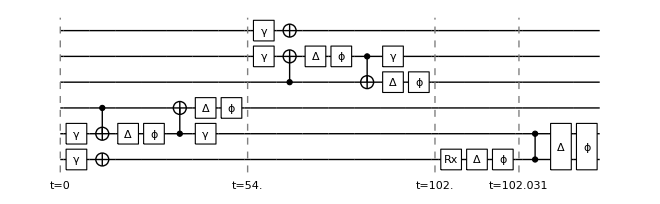

1.

```mathematica
SetQuregMatrix[ρ,RandomMixState[6]];
noisycirc=GetNoisyForm[{Subscript[Init, 0,1,2],Subscript[Init, 3,4,5],Subscript[Rx, 0][π/2],Subscript[C, 0][Subscript[Z, 1]]},SiliconDelft[]];
ApplyCircuit[ρ,ExtractCircuit@noisycirc];
DrawCircuit@noisycirc
ApplyCircuit[InitZeroState@ψ,{Subscript[X, 0],Subscript[X, 5],Subscript[Rx, 0][π/2],Subscript[C, 0][Subscript[Z, 1]]}];
CalcFidelity[ρ,ψ]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
dev=SiliconDelft[];
```

```mathematica
DestroyAllQuregs[];
conf=checkedConf[dev,unitary,5,{3,4,5}];
sidelftclean={};
```

Compilation with automatically generated ansatz at Tue 20 Sep 2022 15:18:46

@cycle1:Tue 20 Sep 2022 15:23:49, fev:237, <E>: 0.10971633361921533 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 1, 90}

I'm slowing down @cycle 2

@cycle2:Tue 20 Sep 2022 15:25:38, fev:306, <E>: 0.10971633361921533 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 1, 124}

@cycle3:Tue 20 Sep 2022 15:46:37, fev:937, <E>: 0.06574975864454212 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 6, 206}

@cycle4:Tue 20 Sep 2022 16:14:28, fev:1576, <E>: 0.010996738336422323 nansatz: 36 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 8, 272}

I'm slowing down @cycle 5

@cycle5:Tue 20 Sep 2022 16:24:44, fev:1746, <E>: 0.010996738336422323 nansatz: 36 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 8, 332}

@cycle6:Tue 20 Sep 2022 17:34:45, fev:2773, <E>: 3.693297279355745e-6 nansatz: 38 merged-smallθ-metric-bf-gmerged: {0, 54, 0, 13, 444}

I'm slowing down @cycle 7

@cycle7:Tue 20 Sep 2022 18:41:42, fev:3425, <E>: 3.693297279355745e-6 nansatz: 38 merged-smallθ-metric-bf-gmerged: {0, 54, 0, 13, 519}

I'm slowing down @cycle 8

@cycle8:Tue 20 Sep 2022 19:14:04, fev:3746, <E>: 3.693297279355745e-6 nansatz: 38 merged-smallθ-metric-bf-gmerged: {0, 54, 0, 13, 600}

compile time:2040.21 minutes; total iterations 3843

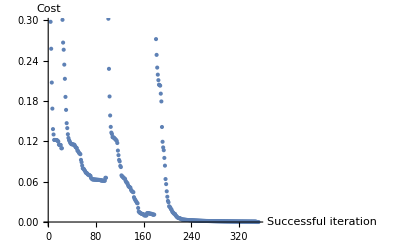

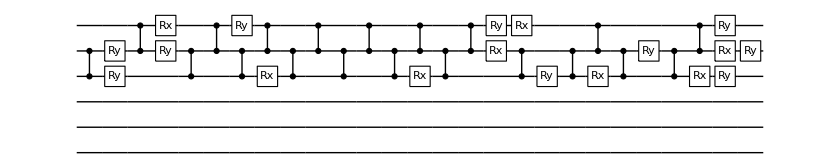

prob(0):<|3→0.333332,4→0.333334,5→0.333334|>

dist_fid=0.999452

Compilation with automatically generated ansatz at Tue 20 Sep 2022 19:18:24

@cycle1:Wed 21 Sep 2022 00:13:08, fev:1963, <E>: 0.000017871702039262694 nansatz: 45 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 12, 392}

I'm slowing down @cycle 2

@cycle2:Wed 21 Sep 2022 00:57:05, fev:2373, <E>: 0.000017871702039262694 nansatz: 45 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 12, 486}

I'm slowing down @cycle 3

@cycle3:Wed 21 Sep 2022 02:47:21, fev:2876, <E>: 0.000017871702039262694 nansatz: 45 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 12, 688}

compile time:2777.02 minutes; total iterations 3000

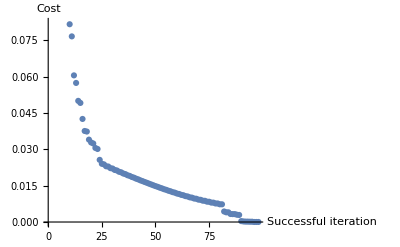

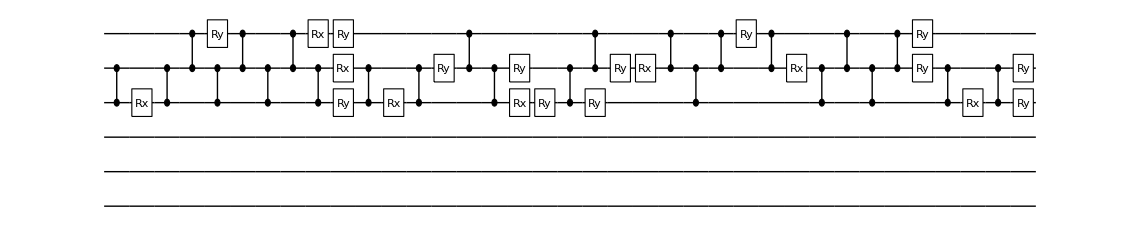

prob(0):<|3→0.333331,4→0.333335,5→0.333335|>

dist_fid=0.999442

Compilation with automatically generated ansatz at Wed 21 Sep 2022 02:52:15

$Aborted

```mathematica
Table[
CompileCirc[conf,unitary,6,sidelftclean]
,{3}]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
```

Use the parameter shift

Compilation with automatically generated ansatz at Wed 21 Sep 2022 12:14:47

@cycle1:Wed 21 Sep 2022 12:53:15, fev:2881, <E>: 0.08478223922086343 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 2, 81}

@cycle2:Wed 21 Sep 2022 13:18:46, fev:4316, <E>: 0.0846123499266929 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 4, 118}

@cycle3:Wed 21 Sep 2022 14:00:49, fev:6224, <E>: 0.008938627884143768 nansatz: 32 merged-smallθ-metric-bf-gmerged: {1, 21, 0, 4, 154}

@cycle4:Wed 21 Sep 2022 14:33:27, fev:7677, <E>: 1.5071275042077837e-6 nansatz: 33 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 4, 192}

I'm slowing down @cycle 5

@cycle5:Wed 21 Sep 2022 14:53:21, fev:8452, <E>: 1.5071275042077837e-6 nansatz: 33 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 4, 218}

I'm slowing down @cycle 6

@cycle6:Wed 21 Sep 2022 15:50:38, fev:10159, <E>: 1.5071275042077837e-6 nansatz: 33 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 4, 276}

simulation time:250.617 min; total iterations 12035

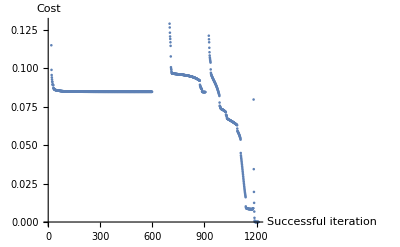

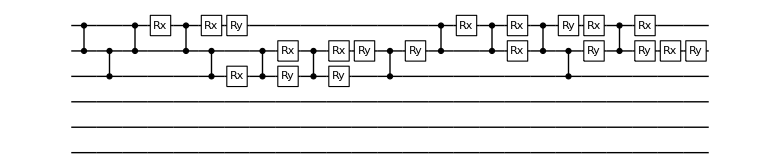

cost:1.50713×10^-6

dist_fid=0.999448

Compilation with automatically generated ansatz at Wed 21 Sep 2022 16:25:26

$Aborted

```mathematica
Table[
DestroyAllQuregs[];
dev=SiliconDelft[];
conf=checkedConf[dev,unitary,5,{3,4,5}];
conf["grad"]="GPS";
CompileCirc[conf,unitary,6,sidelftclean]
,{3}]
```

Parameter shift has a similar performance as the natural gradient. But twice as faster.